Constantes y MaTeX

```mathematica
<<MaTeX`
ℏSI=1.054571817*10^-10;"N*nm*fs";
hEV=4.135667731;"eV*fs";
ℏEV=hEV/(2π);
cUA=299.792458; "nm/fs";
qSI=1.602176565*10^-19;"Coulombs";
ℏcUA=ℏEV*cUA; "eV*nm";
ℏcSI=ℏSI*cUA;"N*(nm)^2";
αEF=0.0072973525693;
UF=ℏcSI*αEF;"N*(nm)^2";

Rojo=RGBColor[0.65,0.25,0.22];
Cian=RGBColor[0.02,0.86,0.95];
Azul=RGBColor[0.02,0.47,0.75];
Verde=RGBColor[0,0.48,0.45];
Amarillo=RGBColor[1,0.7059,0];
```

MaTeX::shdw: Symbol MaTeX appears in multiple contexts {MaTeX`,Global`}; definitions in context MaTeX` may shadow or be shadowed by other definitions.

Funciones auxiliares y materiales

```mathematica
γvel[β_]:=1/(√(1-β^2));
RR[x_,y_,b_]:=√((x-b)^2+y^2);
ϵAlDrude[ℏω_,ℏωp_,ℏΓ_]:=1-(ℏωp)^2/(ℏω*(ℏω+ⅈ*ℏΓ));
γvel[β_]:=1/(√(1-β^2));
konda[ℏω_]:=ℏω/ℏcUA;
xtam[ℏω_,a_]:=a*konda[ℏω];
ℏa[ℏΓ_,ℏω_]:=ℏω/(√2)√(√(1+(ℏΓ/ℏω)^2)+1)+ⅈ*ℏω/(√2)√(√(1+(ℏΓ/ℏω)^2)-1);
wFaddeeva[z_]:=Exp[-z^2]*Erfc[-ⅈ*z];
χBB[ℏωp_,f_,ℏΓ_,ℏω0_,σ_,ℏω_]:=((ⅈ*f*ℏωp^2*√π)/(2 √2*ℏa[ℏΓ,ℏω]*σ))*(wFaddeeva[(ℏa[ℏΓ,ℏω]-ℏω0)/(√2*σ)]+wFaddeeva[(ℏa[ℏΓ,ℏω]+ℏω0)/(√2*σ)]);
χLTZ[ℏωp_,f_,ℏΓ_,ℏω0_,ℏω_]:=(ℏωp^2*f)/(ℏω0^2-ℏω^2-ⅈ*ℏω*ℏΓ);
DataDLAu={{113.1,0.2,0},{44.6,1.5,4},{54.8,3.3,7.3},{184.9,11.8,12.8},{728.1,71,18.9},{65.7,2.9,19.9},{50,3.9,29.9},{74.7,13,38.7},{544,51.9,64.3}};
DataBBBi={{9.541*10^-1,9.889*10^-2,0,0},{2.573*10^-1,1.896,3.877,10^-3},{1.291*10^-1,1.1*10^-3,10^-1,10^-3},{2.559*10^-1,1.155,6.419,1.196},{1.84*10^-1,10^-3,1.062*10,2.094},{4.064*10^-1,3.472,1.239*10,4.042},{1.568,1.126,5.431*10,5},{1.875,1.1*10^-3,7.863*10,5},{5.619*10^-2,4.924*10^-1,2.414*10,1.11*10^-1},{2.852*10^-1,2.141,2.778*10,4.083},{6.089*10^-2,1.1*10^-3,2.75*10,7.08*10^-1},{1.151,1.501,4.094*10,4.414},{8.386*10^-1,8.498*10^-2,6.472*10,4.346}};
DataBBSiC={{3.184*10^-4,5.893*10^-4,9.832*10^-2,0},{3.941*10^-2,2.042*10^-1,6.609,1.077*10^-1},{1.386*10^-2,1.426*10^-4,7.965,1.885*10^-1},{4.353*10^-2,4.687,3.500,2.700*10^-2},{1.042*10^-1,7.812*10^-1,7.487,2.482*10^-2},{1.121,3.305*10^-1,7.101,6.155*10^-1},{7.599*10^-2,9.459*10^-5,1.385*10^1,1.399},{1.553,5.689,1.032*10^1,1.088},{8.240*10^-1,2.153,9.035,4.527*10^-1},{3.624*10^-1,5.376,1.691*10^1,1.082},{3.258*10^-1,3.766,3.081*10^1,3.973},{1.556*10^-2,3.806*10^-5,9.416,2.242*10^-1}};
ϵAuDL[ℏω_]:=1+Sum[χLTZ[1,DataDLAu[[i,1]],DataDLAu[[i,2]],DataDLAu[[i,3]],ℏω],{i,1,9}]
ϵBiBB[ℏω_]:=1+χLTZ[10,DataBBBi[[1,1]],DataBBBi[[1,2]],DataBBBi[[1,3]],ℏω]+Sum[χBB[10,DataBBBi[[i,1]],DataBBBi[[i,2]],DataBBBi[[i,3]],DataBBBi[[i,4]],ℏω],{i,2,13}];
ϵSiCBB[ℏω_]:=1+χLTZ[10,DataBBSiC[[1,1]],DataBBSiC[[1,2]],DataBBSiC[[1,3]],ℏω]+Sum[χBB[10,DataBBSiC[[i,1]],DataBBSiC[[i,2]],DataBBSiC[[i,3]],DataBBSiC[[i,4]],ℏω],{i,2,12}];
Nmat[1,ℏω_]:=√ϵAlDrude[ℏω,13.14,0.197];
Nmat[2,ℏω_]:=√ϵAuDL[ℏω];"Corroborar el calculo";
Nmat[3,ℏω_]:=√ϵBiBB[ℏω];
Nmat[4,ℏω_]:=√ϵSiCBB[ℏω];
```

Funciones especiales

```mathematica
DLAF[l_,m_,x_]:=(l-m+1)/(x^2-1)LegendreP[l+1,m,x]-(l+1)x/(x^2-1)LegendreP[l,m,x];
DSBJ[l_,ρ_]:=(l/(2l+1))SphericalBesselJ[l-1,ρ]-((l+1)/(2l+1))SphericalBesselJ[l+1,ρ];
DSHP[l_,ρ_]:=(l/(2l+1))SphericalHankelH1[l-1,ρ]-((l+1)/(2l+1))SphericalHankelH1[l+1,ρ]

Hplus[l_,ρ_]:=ⅈ*SphericalHankelH1[l,ρ];
DHplus[l_,ρ_]:=ⅈ*DSHP[l,ρ];

psi[l_,ρ_]:=ρ*SphericalBesselJ[l,ρ];
Dpsi[l_,ρ_]:=ρ*DSBJ[l,ρ]+SphericalBesselJ[l,ρ];
xi[l_,ρ_]:=ρ*Hplus[l,ρ];
Dxi[l_,ρ_]:=ρ*DHplus[l,ρ]+Hplus[l,ρ];
```

Coeficientes de Mie

```mathematica
tlE[l_,mat_,ω_,a_]:=(-(Nmat[mat,ℏEV*ω]*psi[l,Nmat[mat,ℏEV*ω]*xtam[ℏEV*ω,a]]*Dpsi[l,xtam[ℏEV*ω,a]]-psi[l,xtam[ℏEV*ω,a]]*Dpsi[l,Nmat[mat,ℏEV*ω]*xtam[ℏEV*ω,a]]))/(Nmat[mat,ℏEV*ω]*psi[l,Nmat[mat,ℏEV*ω]*xtam[ℏEV*ω,a]]*Dxi[l,xtam[ℏEV*ω,a]]-xi[l,xtam[ℏEV*ω,a]]*Dpsi[l,Nmat[mat,ℏEV*ω]*xtam[ℏEV*ω,a]]);
tlM[l_,mat_,ω_,a_]:=(-(psi[l,Nmat[mat,ℏEV*ω]*xtam[ℏEV*ω,a]]*Dpsi[l,xtam[ℏEV*ω,a]]-Nmat[mat,ℏEV*ω]*psi[l,xtam[ℏEV*ω,a]]*Dpsi[l,Nmat[mat,ℏEV*ω]*xtam[ℏEV*ω,a]]))/(psi[l,Nmat[mat,ℏEV*ω]*xtam[ℏEV*ω,a]]*Dxi[l,xtam[ℏEV*ω,a]]-Nmat[mat,ℏEV*ω]*xi[l,xtam[ℏEV*ω,a]]*Dpsi[l,Nmat[mat,ℏEV*ω]*xtam[ℏEV*ω,a]]);
```

Parámetros para IFFT

```mathematica
t0=0;
tN=1500.0;
Npuntos=2^23; "Para la FFT es necesario que sea una potencia de 2"; "Una foto aproximadamente cada 5 attosegundos con tN=5 y Npuntos=2^11";
δt=(tN-t0)/Npuntos;
δω=2π/(tN-t0);
tiempo=Table[(j-(Npuntos/2))*δt,{j,1,Npuntos}]+$MachineEpsilon;
frecuencias=Table[(j-(Npuntos/2))*δω,{j,1,Npuntos}]+$MachineEpsilon;
TablaCero=Table[0,{l,1,Npuntos}];
frecuencias[[Npuntos]]
δω
```

17569.1

0.00418879

Funciones espectrales del campo EM esparcido lejano

```mathematica
ΩEtilde[l_,m_,mat_,r_,ω_,β_,a_,b_]:=Piecewise[{{tlE[l,mat,ω,a]*BesselK[m,(ℏEV*ω*b)/(ℏcUA*β*γvel[β])]*Exp[ⅈ*konda[ℏEV*ω]*r],ω>=0},{Conjugate[tlE[l,mat,-ω,a]*BesselK[m,(-ℏEV*ω*b)/(ℏcUA*β*γvel[β])]*Exp[ⅈ*konda[-ℏEV*ω]*r]],ω<0}}];
ΩMtilde[l_,m_,mat_,r_,ω_,β_,a_,b_]:=Piecewise[{{tlM[l,mat,ω,a]*BesselK[m,(ℏEV*ω*b)/(ℏcUA*β*γvel[β])]*Exp[ⅈ*konda[ℏEV*ω]*r],ω>=0},{Conjugate[tlM[l,mat,Abs[ω],a]*BesselK[m,(ℏEV*Abs[ω]*b)/(ℏcUA*β*γvel[β])]*Exp[ⅈ*konda[ℏEV*Abs[ω]]*r]],ω<0}}];
```

Transformadas de Fourier inversas de las funciones espectrales auxiliares del campo EM esparcido lejano

```mathematica
ΩM[l_,m_,mat_,r_,β_,a_,b_]:=
(δω/(2π))*Chop[RotateRight[InverseFourier[RotateLeft[ParallelTable[ΩMtilde[l,m,mat,r,frecuencias[[j]],β,a,b],{j,1,Npuntos}],(Npuntos/2)-1],FourierParameters->{-1,1}],(Npuntos/2)-1]];
ΩE[l_,m_,mat_,r_,β_,a_,b_]:=(δω/(2π))*Chop[RotateRight[InverseFourier[RotateLeft[ParallelTable[ΩEtilde[l,m,mat,r,frecuencias[[j]],β,a,b],{j,1,Npuntos}],(Npuntos/2)-1],FourierParameters->{-1,1}],(Npuntos/2)-1]];
```

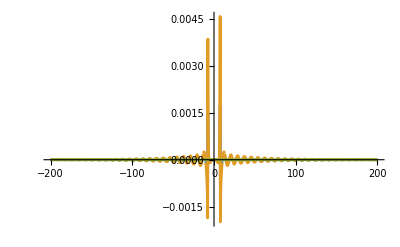

```mathematica
Plot[{Re[ΩEtilde[1,0,1,cUA/2,ω/ℏEV,0.58,1,4]],Re[ΩEtilde[1,1,1,cUA/2,ω/ℏEV,0.58,1,4]],Re[ΩMtilde[1,1,1,cUA/2,ω/ℏEV,0.58,1,4]]},{ω,-200,200},PlotRange->All]
```

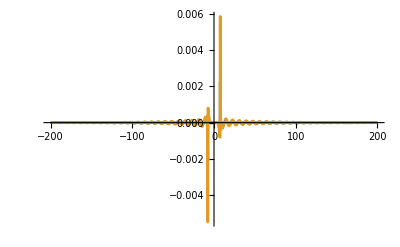

```mathematica
Plot[{Im[ΩEtilde[1,0,1,cUA/2,ω/ℏEV,0.58,1,4]],Im[ΩEtilde[1,1,1,cUA/2,ω/ℏEV,0.58,1,4]],Im[ΩMtilde[1,1,1,cUA/2,ω/ℏEV,0.58,1,4]]},{ω,-200,200},PlotRange->All]
```

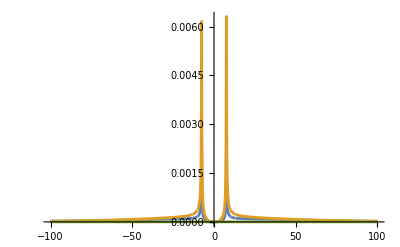

```mathematica
Plot[{Abs[ΩEtilde[1,0,1,cUA/2,ω/ℏEV,0.58,1,4]],Abs[ΩEtilde[1,1,1,cUA/2,ω/ℏEV,0.58,1,4]],Abs[ΩMtilde[1,1,1,cUA/2,ω/ℏEV,0.58,1,4]]},{ω,-100,100},PlotRange->All]
```

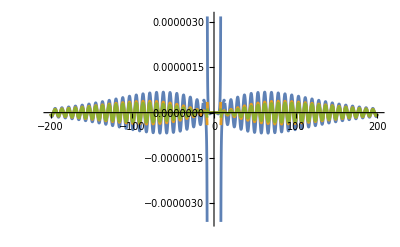

```mathematica
Plot[{Re[ΩEtilde[2,2,1,cUA/2,ω/ℏEV,0.58,1,4]],Re[ΩEtilde[2,1,1,cUA/2,ω/ℏEV,0.58,1,4]],Re[ΩEtilde[2,0,1,cUA/2,ω/ℏEV,0.58,1,4]]},{ω,-200,200},PlotRange->All]
```

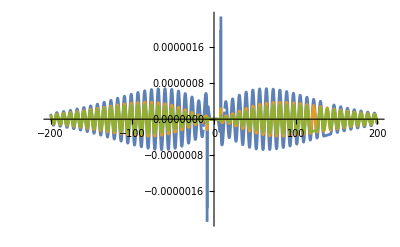

```mathematica
Plot[{Im[ΩEtilde[2,2,1,cUA/2,ω/ℏEV,0.58,1,4]],Im[ΩEtilde[2,1,1,cUA/2,ω/ℏEV,0.58,1,4]],Im[ΩEtilde[2,0,1,cUA/2,ω/ℏEV,0.58,1,4]]},{ω,-200,200},PlotRange->All]
```

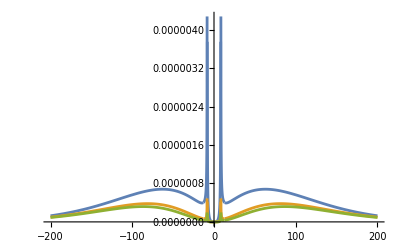

```mathematica
Plot[{Abs[ΩEtilde[2,2,1,cUA/2,ω/ℏEV,0.58,1,4]],Abs[ΩEtilde[2,1,1,cUA/2,ω/ℏEV,0.58,1,4]],Abs[ΩEtilde[2,0,1,cUA/2,ω/ℏEV,0.58,1,4]]},{ω,-200,200},PlotRange->All]
```

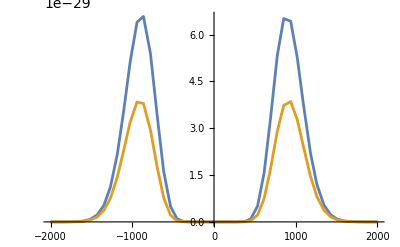

```mathematica
Plot[{Abs[ΩMtilde[15,15,1,cUA/2,ω/ℏEV,0.58,1,4]],Abs[ΩMtilde[15,14,1,cUA/2,ω/ℏEV,0.58,1,4]]},{ω,-2000,2000},PlotRange->All]
```

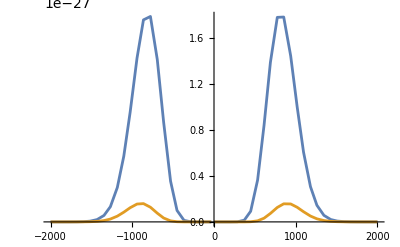

```mathematica
Plot[{Abs[ΩEtilde[15,15,1,cUA/2,ω/ℏEV,0.58,1,4]],Abs[ΩEtilde[15,10,1,cUA/2,ω/ℏEV,0.58,1,4]]},{ω,-2000,2000},PlotRange->All]
```

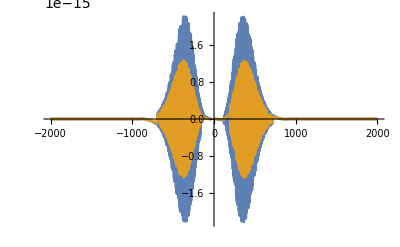

```mathematica
Plot[{Re[ΩEtilde[7,7,1,cUA/2,ω/ℏEV,0.58,1,4]],Re[ΩEtilde[7,6,1,cUA/2,ω/ℏEV,0.58,1,4]]},{ω,-2000,2000},PlotRange->All]
```

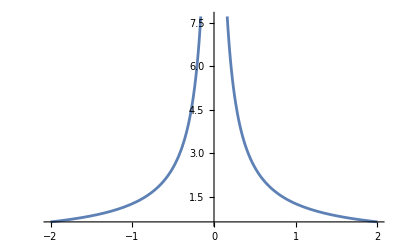

```mathematica
Plot[Experimento[0,cUA,0.58,3,t],{t,-2,2}]
```

```mathematica
1000*331*10^-6//N
```

0.331

```mathematica
data=Import["/home/eduardo/Documentos/Universidad/Maestría/Cálculos/FFTW/bessel_results.txt","table"];
Dimensions[data]
```

{200,3}

```mathematica
FuncionPrueba[n_,x_]:=(SphericalBesselJ[n,x]*x+SphericalBesselY[n,x]*x)/(SphericalBesselJ[n,x]*x-SphericalBesselY[n,x]*x)*BesselK[n,x];
```

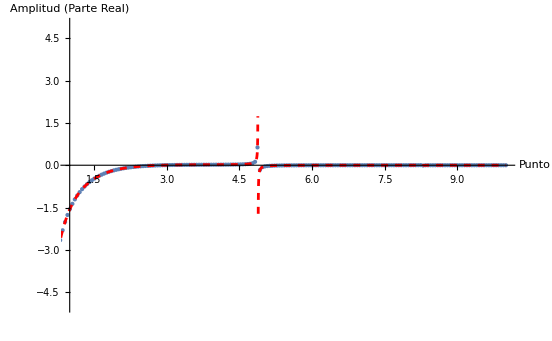

```mathematica
(*Graficar la parte real de los resultados*)realPlot=ListPlot[Transpose[{data[[All,1]],data[[All,2]]}],PlotRange->{{1,10},{-5,5}},PlotStyle->PointSize[Medium],AxesLabel->{"Punto","Amplitud (Parte Real)"},Joined->False];
Show[realPlot,Plot[Re[FuncionPrueba[2,x]],{x,0,10},PlotStyle->{Red,Dashed},PlotPoints->40,PlotRange->{-5,5}]]
```